```mathematica
freqList={309.28, 403.96, 468.56,647.07,679.85,8.14.31, 840.42,937.85,939.83, 943.95}*10^-6;
lList={2,1,3,4,2,0,5,2,3,1};
nList={0,2,0,0,1,0,0,2,1,3};
qList=1000/{1.962,2.52,2.395,2.680,3.222,0.188, 2.812,10.432,3.537,1.209};
```

```mathematica
M=5.972*10^24; 
ρ=5515;
α= 10^4;
β = 10^4;
c=3*10^8;
h=6.6*10^-34/2/Pi;
R=6371*10^3;
u=7.6*10^-8;
p=10^-3*ω/(2 Pi c);
q=ω/α;
```

```mathematica
D[SphericalBesselJ[0,z],z]/.{z->q r};
NIntegrate[Conjugate[%]*%r^2,{r,0,R}];
cn=Sqrt[M/(4Pi%*ρ)];
```

NIntegrate::inumr: The integrand r^2 Conjugate[-(5000 SphericalBesselJ[0,(r ω)/10000])/(r ω)+1/2 (SphericalBesselJ[-1,(r ω)/10000]-SphericalBesselJ[1,Times[«3»]])] (-(5000 SphericalBesselJ[0,(r ω)/10000])/(r ω)+1/2 (SphericalBesselJ[-1,(r ω)/10000]-SphericalBesselJ[1,(r ω)/10000])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6371000}}.

```mathematica
D[SphericalBesselJ[0,z],z]/.{z->q r};
int=NIntegrate[%*SphericalBesselJ[1,p r]r^2,{r,0,R}]
f=Sqrt[3]M u/( Q(4Pi)cn%SphericalHarmonicY[1,0,0,0])
```

-1.20197×10^10

-8.17332×10^-19

```mathematica
l>0
```

False

```mathematica
Clear[lMode]
Clear[ω]
Clear[Q]
```

l | m | Integral
2 | 0 | 2.77086×10^18
1 | 2 | 3.44691×10^26
3 | 0 | 1.24452×10^10
4 | 0 | 38.9486
2 | 1 | 2.78481×10^18
0 | 0 | 4.72578×10^11
5 | 0 | 9.37308×10^-8
2 | 2 | 2.77696×10^18
3 | 1 | 1.24727×10^10
1 | 3 | 3.34672×10^26

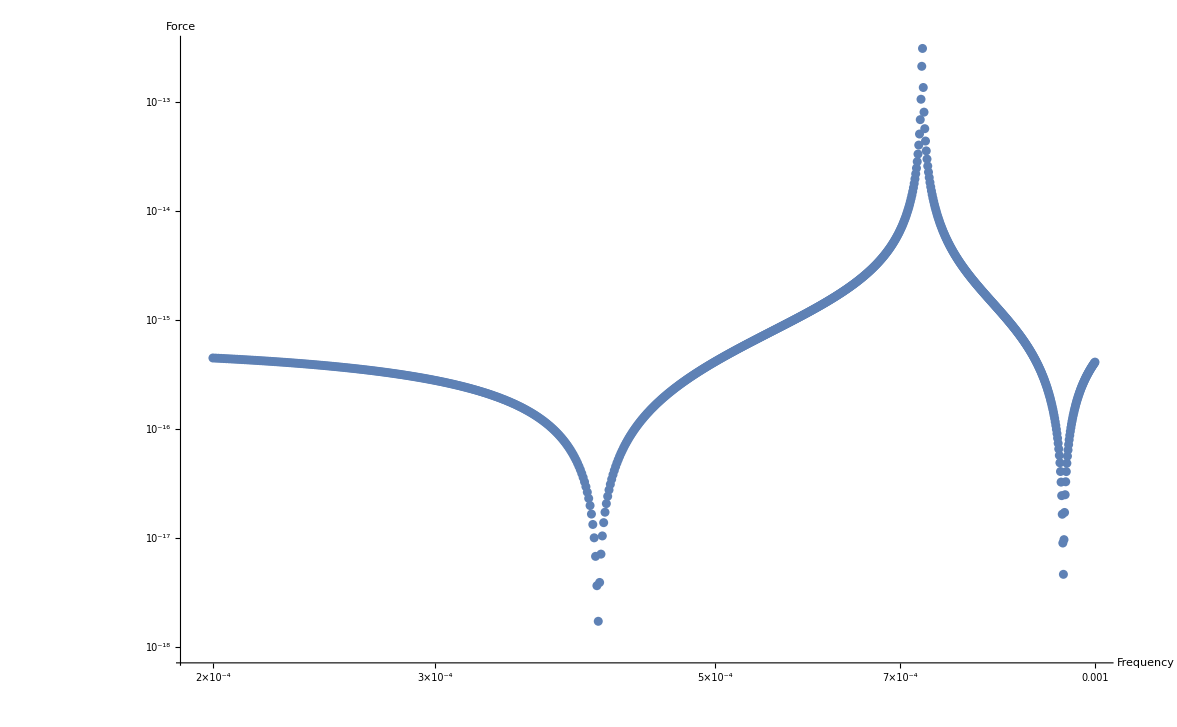

```mathematica
M=5.972*10^24; 
ρ=5515;
α= 10^4;
β = 10^4;
c=3*10^8;
h=6.6*10^-34/2/Pi;
R=6371*10^3;
u=7.6*10^-8;
ωSpec=2*Pi*Range[200,1000,1]*10^-6;
spec={};
ProgressIndicator[Dynamic[index/Length[ωSpec]]]
For[index=1,index≤Length[ωSpec], index++,
intList={};
Quiet[For[modeIndex=1,modeIndex≤Length[lList], modeIndex++,
lMode=lList[[modeIndex]];
ωMode=2*Pi*freqList[[modeIndex]];
Q=qList[[modeIndex]];
lRange=10;
aAngularInt=Table[Integrate[SphericalHarmonicY[lMode,0,θ,ϕ]*Conjugate[SphericalHarmonicY[l,0,θ,ϕ]]*Cos[θ]*Sin[θ],{θ,0,Pi},{ϕ,0,2*Pi}],{l,0,lRange}];
bAngularInt=Table[Integrate[D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]*Conjugate[SphericalHarmonicY[l,0,θ,ϕ]]*Sin[θ]*Sin[θ],{θ,0,Pi},{ϕ,0,2*Pi}],{l,0,lRange}];
p=10^-3*ωSpec[[index]]/(2 Pi c);
q=ωMode/α;
k=ωMode/β;
alpha=0.5*((D[D[SphericalBesselJ[lMode,z],z],z]/.{z->k R})+(lMode-1)(lMode+2)(SphericalBesselJ[lMode,z]/.{z->k R})/(k R)^2);
beta=N[q/k D[SphericalBesselJ[lMode,z]/z,z]/.{z->q R}];
a=alpha*(D[SphericalBesselJ[lMode,z],z]/.{z->q r})-beta*lMode*(lMode+1)SphericalBesselJ[lMode,k r]/(k r);
b=r/R(alpha*SphericalBesselJ[lMode,q r]/(q /r)-beta (SphericalBesselJ[lMode,k r]/(k r)+D[SphericalBesselJ[lMode,z],z]/.{z->k r}));
cn=Sqrt[M/ρ /NIntegrate[(a^2*Conjugate[SphericalHarmonicY[lMode,0,θ,ϕ]]*SphericalHarmonicY[lMode,0,θ,ϕ]
+b^2 R^2 (1/r^2 Conjugate[D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]]*D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]+
1/r^2 /Sin[θ]^2Conjugate[D[SphericalHarmonicY[lMode,0,θ,ϕ],ϕ]]*D[SphericalHarmonicY[lMode,0,θ,ϕ],ϕ]))
r^2 Sin[θ],{r,0,R},{θ,0,Pi},{ϕ,0,2*Pi}]];
int=NIntegrate[(aAngularInt*a*Table[I^lBes SphericalHarmonicY[lBes,0,0,0] SphericalBesselJ[lBes,p r],{lBes,0,lRange}]+R*bAngularInt*b*Table[I^lBes SphericalHarmonicY[lBes,0,0,0]SphericalBesselJ[lBes,p r],{lBes,0,lRange}])r^2,{r,0,R}];
intList=Append[intList,cn Total[int]];
];
spec=Append[spec,M*u/Total[(4 Pi I intList)/(4*Pi^2*freqList^2-ωSpec[[index]]^2+I*ωSpec[[index]]*2*Pi*freqList/qList)]];
]]
Grid[Prepend[Transpose[{lList,nList,Abs[intList]}],{"l","m","Integral"}]]
ListLogLogPlot[Transpose[{ωSpec/(2*Pi), Abs[spec]}],AxesLabel->{"Frequency","Force/m^3"}]
```

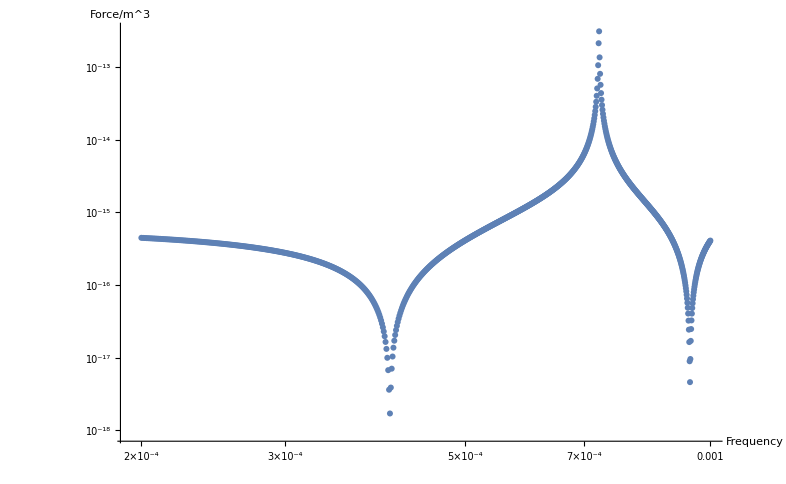

```mathematica
ListLogLogPlot[Transpose[{ωSpec/(2*Pi), Abs[spec]}],AxesLabel->{"Frequency","Force/m^3"}]
```